# Signal Processing - Project 2

## William Lewin & Elias Chahine wlewin@kth.se echahine@kth.se

## Part 1

### Assignment

Introduce the system function of an IIR-filter as
H(z)=((1-z^-1)  ∏_(k=1)^4 (1-z^-1 e^(-i (2k-1)(11π)/100))(1-z^-1 e^(i (2k-1)(11π)/100)))/(100 ∏_(k=1)^4 (1-0.9 z^-1 e^(-i k(11π)/50))(1-0.9 z^-1 e^(i k(11π)/50)))

Make a pole-zero plot of H(z). Is the system stable?

Discuss how the filter works, what happens with certain frequencies?

Illustrate the frequency response of the IIR.

Sketch a direct form structure to illustrate the IIR.

Introduce the signal x(t)=1/π∑_(k=1)^9 (-1)^(k-1)/k sin(2 π f_0 k t), f_0=220Hz. This signal is sampled with the frequency f_s=4kHz. Plot the sampled signal x[n].

Now, the signal x[n] is input to the IIR above. Compute and plot the output signal y[n].

Finally, draw and compare the two-sided spectrum of x[n] and y[n].

### Discussion

#### Is the system stable?

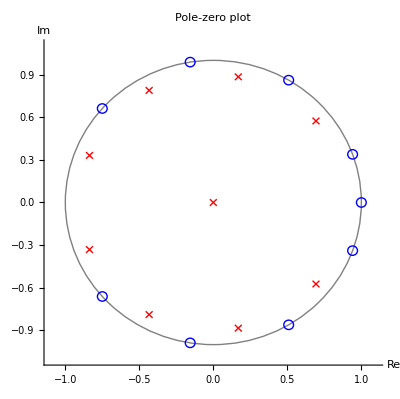
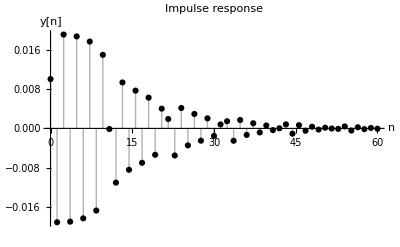
-Graphics-

The system is stable. All the poles are located within the unit circle; meaning that the response signal will weaken with time and not grow to infinity. We can also plot the step response to further display the weakening over time:

-Graphics-

#### Discuss the filters function

The filter works as a high-pass filter of sorts. Some frequencies are even removed completely.

#### Illustrate the frequency response of the IIR

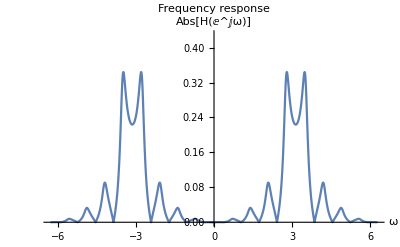
-Graphics-

By plotting the frequency response from ω = - 2π → 2π  we can see how it affects different signals. The filter removes signals with low frequencies, acting as a highpass filter.

#### Sketch a direct form structure to illustrate the IIR

First off, we expand the numerator of the signal to the 9th order, then the denominator by the same procedure. 
Numerator_k = a_k
Denominator_k = b_k
-Graphics-
Numerator_k={1.,-2.08675,2.21423,-2.27535,2.30205,-2.30205,2.27535,-2.21423,2.08675,-1}
Denominator_k={100.,81.6544,77.8267,67.0446,62.7484,54.3061,51.0621,43.3945,43.0467}

#### Introduce a signal, plot the sampled signal x[n]

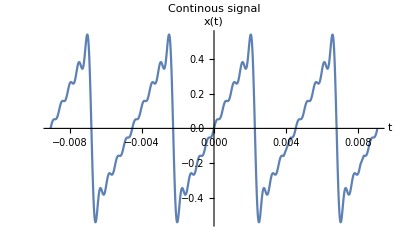
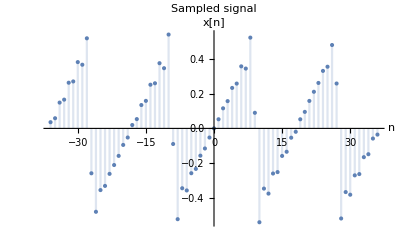
Signal:
-Graphics-
Sampled signal:
-Graphics-

#### Plot the output y[n]

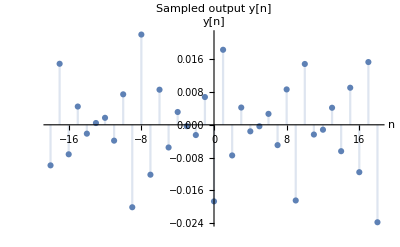
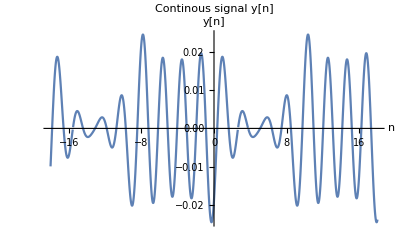
Sampled output signal:
-Graphics-
Continuous output signal:
-Graphics-

#### Draw and compare the two sided spectrum of x[n] and y[n]

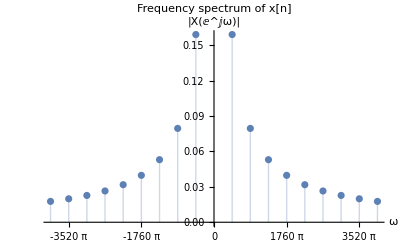
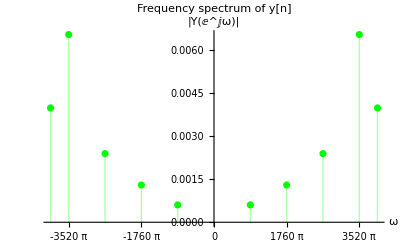
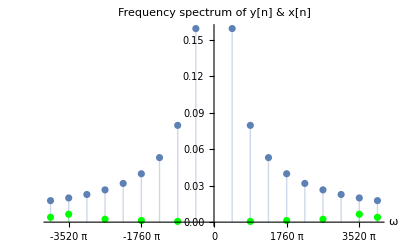
Frequency spectrum of x[n]: 
-Graphics-
Frequency spectrum of y[n]:
-Graphics-
Frequency spectrum of both x[n] and y[n]
-Graphics-

### Code

```mathematica
ClearAll[".b4*"]
```

#### Package II1303

```mathematica
(* Ver. 151125, goeran@kth.se *)
BeginPackage["II1303`"]; 
Unprotect[{ToExp, TrigCombine, PoleZeroPlot, Poles, Zeros, PoleZeroPlot, PoleZeroStyle, 
	ZTransform2, InverseZTransform2, FactorAll, ApartAll, ZApart, LaplaceTransform2, 
	InverseLaplaceTransform2}]; 
Reconstruct::usage = "Reconstruct[fs][{f,A,ϕ}] returns the shifted or folded  \
{f,A,ϕ} list due to sampling. Reconstruct[ωs][{ω,A,ϕ}] is also valid.";
fAϕ::usage = "fAϕ[t][Cos|Sin|Exp[arg]] extracts {f,A,ϕ} information.";
ωAϕ::usage = "ωAϕ[t][Cos|Sin|Exp[arg]] extracts {ω,A,ϕ} information.";
ToExp::usage = "ToExp[z] = Abs[z]*E^(I*Arg[z]) returns a complex number in \
exponential form.\nFor floating point complex numbers use ReleaseHold in orer to \
evaluate."; 
TrigCombine::usage = "ToExp[a*trig[x+α] + b*trig[x+β]], where trig is Cos or Sin, \
returns A*trig[x+v].";
Poles::usage = "Poles[H, z] returns the poles of the system function H[z]."; 
Zeros::usage = "Zeros[H, z] returns the zeros of the system function H[z]."; 
PoleZeroPlot::usage = "PoleZeroPlot[H, z] plots poles and zeros of the system \
function H[z].\nPoleZeroPlot takes the same options as ListPlot."; 
PoleMarker::usage = "PoleMarker is an option for PoleZeroPlot that defines the \
graphics for the pole marker.\nIt is assumed to be a Function[{postition, \
multiplicity, scale}, ...]."; 
ZeroMarker::usage = "ZeroMarker is an option for PoleZeroPlot that defines the \
graphics for the zero marker.\nIt is assumed to be a Function[{postition, \
multiplicity, scale}, ...].";
MarkerScale::usage = "MarkerScale is an option for PoleZeroPlot that defines the \
scale for the pole and zero marker."; 
ZTransform2::usage = "ZTransform2[x, n, z] returns the bilateral, 1D z-transform.\n\
It evaluates FourierSequenceTransform[x,n,-I Log[z]]."; 
InverseZTransform2::usage = "InverseZTransform2[X, z, n] returns the bilateral, 1D \
inverse z-transform.\nIt evaluates InverseFourierSequenceTransform[X /. z -> \
E^(I*ω), ω, n]."; 
FactorAll::usage = "FactorAll[p, x] returns a product of first degree factors."; 
ZApart::usage = "ZApart[X, z] = Expand[z*Apart[X/z,z]] returns an expression \
suitable for inverse z-transform."; 
LaplaceTransform2::usage = "LaplaceTransform2[x, t, s] returns the bilateral, 1D \
Laplace transform.\nIt evaluates FourierTransform[x, t, -I*s]."; 
InverseLaplaceTransform2::usage = "InverseLaplaceTransform2[X, s, t] returns the \
bilateral, 1D inverse Laplace transform.\nIt evaluates InverseFourierTransform[X /. \
s -> I*ω, ω, t].";
 
Begin["`Private`"];
Reconstruct[(fs_)?Positive][{f_,A_,ϕ_}]:=
Module[
	{fa,ϕa=ϕ},
	(* shift *)
	fa=Mod[Abs[f], fs];
	(* fold *)
	If[fa>fs/2,fa=fs-fa;ϕa=-ϕ];
	If[fa>0,{Sign[f]*fa,A,ϕa},{0,A,ϕa}]
];

Reconstruct[fs_][data:{{_, _, _}..}] := 
Module[{data1,data2,data3}, 
	data1 = Reconstruct[fs] /@ data;
	data2 = Gather[data1, #1[[1]] == #2[[1]] & ];
	({#1[[1,1]], Norm[#1[[All,2]] . E^(I*#1[[All,3]])], Arg[#1[[All,2]] . E^(I*#1[[All,3]])]} & ) /@ data2
];

fAϕ[t_Symbol][(A_:1)Cos[x_]]:={Coefficient[x,t]/(2π),Abs[A],Coefficient[x,t,0]+Arg[A]};
fAϕ[t_Symbol][(A_:1)Sin[x_]]:={Coefficient[x,t]/(2π),Abs[A],Coefficient[x,t,0]-π/2+Arg[A]};
fAϕ[t_Symbol][(A_:1)Exp[z_]]:={Coefficient[z,t]/(2π ⅈ),Abs[A],Coefficient[z,t,0]/ⅈ+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Cos[x_]]:={Coefficient[x,t],Abs[A],Coefficient[x,t,0]+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Sin[x_]]:={Coefficient[x,t],Abs[A],Coefficient[x,t,0]-π/2+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Exp[z_]]:={Coefficient[z,t]/ⅈ,Abs[A],Coefficient[x,t,0]/ⅈ+Arg[A]};
 
ToExp[z:Complex[_Real, _Real]] := Abs[z]*HoldForm[E]^(I*Arg[z]); 
ToExp[(z_)?NumericQ] := Abs[z]*E^(I*Arg[z]); 
ToExp[z___] := z; 
SetAttributes[ToExp, Listable];

TrigCombine[(a_:1)*Cos[(x_) + (u_:0)] + (b_:1)*Cos[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) + b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[a*E^(I*u) + b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
TrigCombine[(a_:1)*Cos[(x_) + (u_:0)] + (b_:1)*Sin[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) - I*b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[a*E^(I*u) - I*b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
TrigCombine[(a_:1)*Sin[(x_) + (u_:0)] + (b_:1)*Sin[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) + b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[(-I)*a*E^(I*u) - I*b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
SetAttributes[TrigCombine, HoldAll];

Poles[H_, z_Symbol] := Flatten[
	TransferFunctionPoles[TransferFunctionCancel[TransferFunctionModel[H, z]]]
]; 
Poles[H:_Symbol | _Function, z_Symbol] := Poles[H[z], z];
 
Zeros[H_, z_Symbol] := Flatten[
TransferFunctionZeros[TransferFunctionCancel[TransferFunctionModel[H, z]]]
]; 
Zeros[H:_Symbol | _Function, z_Symbol] := Zeros[H[z], z];
 
Options[PoleZeroPlot] = Join[{
	PoleMarker :> ({
		Red, 
		Line[{#1 + #3*{-1, -1}/√2, #1 + #3*{1, 1}/√2}], 
		Line[{#1 + #3*{-1, 1}/√2, #1 + #3*{1, -1}/√2}], 
		If[#2 > 1, Text[#2, #1 + #3*{√2, √2}, {-1, 0}], Sequence @@ {}]} & ), 
	ZeroMarker :> ({
		Blue, 
		Circle[#1, #3], 
        If[#2 > 1, Text[#2, #1 + #3*{√2, √2}, {-1, 0}], Sequence @@ {}]} & ),
	MarkerScale -> Automatic
	}, 
	Options[Graphics]
]; 
SetOptions[PoleZeroPlot, AspectRatio -> Automatic, Axes -> True, PlotRange -> Automatic]; 
PoleZeroPlot[H_, z_Symbol, opts:OptionsPattern[]] := Module[
	{xy, x, y, d, pp, pz, mp, mz, s, r, 𝕡, 𝕫, range, allopts, s0=Scaled[0.015]}, 
	xy := {Re[#1], Im[#1]} & ; 𝕡 = Poles[N[H], z]; 𝕫 = Zeros[N[H], z]; 
	pp = xy /@ DeleteDuplicates[𝕡]; pz = xy /@ DeleteDuplicates[𝕫]; 
	mp = Length /@ Gather[𝕡]; mz = Length /@ Gather[𝕫]; 
	x = Join[pz[[All,1]], pp[[All,1]]]; y = Join[pz[[All,2]], pp[[All,2]]]; 
	If[OptionValue[PlotRange] === Automatic, 
		x = Join[{-1, 1}, x]; y = Join[{-1, 1}, y]
	]; 
	range = ({Min[#1], Max[#1]} & ) /@ {x, y}; 
	d = 0.05*Apply[Subtract, range, {1}]; range = range + Transpose[{d, -d}]; 
	allopts = FilterRules[Join[{opts}, Options[PoleZeroPlot]], Options[Graphics]]; 
	If[OptionValue[PlotRange] === Automatic || OptionValue[PlotRange] === All, 
		PrependTo[allopts, PlotRange -> range]
	]; 
	s = OptionValue[MarkerScale];
	If[ s=== Automatic, s = s0];
	If[ ! MatchQ[s, _?NumericQ] && ! MatchQ[s, Scaled[_?NumericQ]], s = s0];
	If[MatchQ[s, Scaled[_?NumericQ]],
		s = First[s];
		r = PlotRange/.AbsoluteOptions[Graphics[Point[Join[pp,pz]],Sequence @@ allopts],PlotRange];
		If[MatchQ[r,{{_?NumberQ,_?NumberQ},{_?NumberQ,_?NumberQ}}],s*=Min[-Subtract@@@r]]
	];
	Graphics[{
		Apply[OptionValue[PoleMarker], (Join[#1, {s}] & ) /@ Transpose[{pp, mp}], {1}], 
		Apply[OptionValue[ZeroMarker], (Join[#1, {s}] & ) /@ Transpose[{pz, mz}], {1}]
		}, Sequence @@ allopts
	]
];
PoleZeroPlot[H:_Symbol | _Function, z_Symbol, opts:OptionsPattern[]] := PoleZeroPlot[H[z], z, opts]; 

Options[ZTransform2] = Rest[Options[FourierSequenceTransform]]; 
ZTransform2[x_, n_Symbol, z_, opts:OptionsPattern[]] := 
	FourierSequenceTransform[x, n, (-I)*Log[z], FourierParameters -> {1, 1}, opts];
ZTransform2[x:_Symbol | _Function, n_Symbol, z_, opts:OptionsPattern[]] := 
	ZTransform2[x[n], n, z, opts]; 

Options[InverseZTransform2] = Rest[Options[InverseFourierSequenceTransform]]; 
InverseZTransform2[X_, z_Symbol, n_, opts:OptionsPattern[]] := Module[{ω}, 
	InverseFourierSequenceTransform[X /. z -> E^(I*ω), ω, n, FourierParameters -> {1, 1}, opts]
]; 
InverseZTransform2[X:_Symbol | _Function, z_Symbol, n_, opts:OptionsPattern[]] := 
	InverseZTransform2[X[z], z, n, opts];

FactorAll[p_, x_Symbol] := Module[
{a, z, q}
, a = Coefficient[p, x, Exponent[p, x]]; 
q = p/a; z = x /. Solve[q == 0, x, Complexes]; 
Times @@ Join[{a}, x - z]
] /; PolynomialQ[p, x];

ZApart[X_, z_Symbol] := Expand[z*Apart[X/z, z]];
 
Options[LaplaceTransform2] = Most[Options[FourierSequenceTransform]]; 
LaplaceTransform2[x_, t_Symbol, s_, opts:OptionsPattern[]] := 
	FourierTransform[x, t, (-I)*s, FourierParameters -> {1, -1}, opts];
LaplaceTransform2[x:_Symbol | _Function, t_Symbol, s_, opts:OptionsPattern[]] := 
	LaplaceTransform2[x[t], t, s, opts]; 

Options[InverseLaplaceTransform2] = Most[Options[InverseFourierSequenceTransform]]; 
InverseLaplaceTransform2[X_, s_Symbol, t_, opts:OptionsPattern[]] := Module[{ω}, 
	InverseFourierTransform[X /. s -> I*ω, ω, t, FourierParameters -> {1, -1}, opts]
]; 
InverseLaplaceTransform2[X:_Symbol | _Function, s_Symbol, t_, opts:OptionsPattern[]] := 
	InverseLaplaceTransform2[X[s], s, t, opts];
 
End[];
 
Protect[{Reconstruct, fAϕ, ωAϕ, ToExp, TrigCombine, PoleZeroPlot, Poles, Zeros, PoleZeroPlot, PoleZeroStyle, 
	ZTransform2, InverseZTransform2, FactorAll, ApartAll, ZApart, LaplaceTransform2, 
	InverseLaplaceTransform2}]; 

EndPackage[];
```

SetDelayed::write: Tag Reconstruct in Reconstruct[fs_?Positive][{f_,A_,ϕ_}] is Protected.

SetDelayed::write: Tag Reconstruct in Reconstruct[fs_][data:{{_,_,_}..}] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][Cos[x_] (A_:1)] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][(A_:1) Sin[x_]] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][ⅇ^z_ (A_:1)] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][Cos[x_] (A_:1)] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][(A_:1) Sin[x_]] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][ⅇ^z_ (A_:1)] is Protected.

#### The rest

```mathematica
H[z_]:=((1-z^-1)∏_(k=1)^4 ((1-z^-1 E^(-ⅉ (2k-1)(11 π)/100)) (1-z^-1 E^(ⅉ (2k-1)(11 π)/100))))/(100∏_(k=1)^4 ((1-0.9 z^-1 E^(-ⅉ k(11 π)/50)) (1-0.9 z^-1 E^(ⅉ k(11 π)/50))))
```

```mathematica
data1=Table[UnitStep[n],{n,0,50,1}]//N;
data2=TransferFunctionModel[{{H[z]}},z,SamplingPeriod->1];
dataTot=OutputResponse[data2,data1];
```

```mathematica
Subscript[Numerator, k]=Reverse[CoefficientList[Expand[Numerator[H[z]]×z^9], z]]//Re//N
Subscript[Denominator, k]=Reverse[CoefficientList[Expand[Denominator[H[z]]×z^8], z]]//Re//N
```

{1.,-2.08675,2.21423,-2.27535,2.30205,-2.30205,2.27535,-2.21423,2.08675,-1.}

{100.,81.6544,77.8267,67.0446,62.7484,54.3061,51.0621,43.3945,43.0467}

```mathematica
(*Plot the sampled signal x[n]*)
f0=220;
fs=4×10^3;
T0=1/f0;
ω̂=f0/fs;
(*x[n] as a input signal and plot the output signal y[n]*)
x1[t_]=1/π×∑_(k=1)^9 ((-1)^(k-1)/k×Sin[2π×k×f0×t]);
x2[n_]=1/π×∑_(k=1)^9 ((-1)^(k-1)/k×Sin[2π×k×ω̂×n]);
```

```mathematica
omegax={-(99π)/100,-(88π)/100,-(77π)/100,-(66π)/100,-(55π)/100,-(44π)/100,-(33π)/100,-(22π)/100,-(11π)/100,(11π)/100,(22π)/100,(33π)/100,(44π)/100,(55π)/100,(66π)/100,(77π)/100,(88π)/100,(99π)/100};
Ax={1/(18π),-1/(16π),1/(14π),-1/(12π),1/(10π),-1/(8π), 1/(6π),-1/(4π),1/(2π),1/(2π),-1/(4π),1/(6π),-1/(8π),1/(10π),-1/(12π),1/(14π),-1/(16π),1/(18π)};
phix={π/2,π/2,π/2,π/2,π/2,π/2,π/2,π/2,π/2,-π/2,-π/2,-π/2,-π/2,-π/2,-π/2,-π/2,-π/2,-π/2};
omegay={-(99π)/100,-(88π)/100,-(66π)/100,-(44π)/100,-(22π)/100,(22π)/100,(44π)/100,(66π)/100,(88π)/100,(99π)/100};
Ay={(0.0002806806031521044+0.0039631408255394645 ⅈ),-(0.006393010574985013-0.0012910074963131584 ⅈ),-(0.0020801354048053107-0.0011656051511536834 ⅈ),-(0.0008825242514179283-0.000945822003078591 ⅈ),-(0.0002832541668169339-0.000532286013614501 ⅈ),-(0.0002832541668169338+0.000532286013614501 ⅈ),-(0.0008825242514179283+0.0009458220030785912 ⅈ),-(0.0020801354048053107+0.0011656051511536834 ⅈ),-(0.006393010574985013+0.0012910074963131584 ⅈ),(0.0002806806031521044-0.0039631408255394645 ⅈ)};
```

```mathematica
X=Ax*E^(ⅉ*phix);
x[n_]=Plus@@(X*E^(ⅉ*omegax*n))
y[n_]=Plus@@(H[E^(ⅉ*omegax)] X E^(ⅉ* omegax *n))
```

(ⅈ ⅇ^(-11/100 ⅈ n π))/(2 π)-(ⅈ ⅇ^((11 ⅈ n π)/100))/(2 π)-(ⅈ ⅇ^(-11/50 ⅈ n π))/(4 π)+(ⅈ ⅇ^((11 ⅈ n π)/50))/(4 π)+(ⅈ ⅇ^(-33/100 ⅈ n π))/(6 π)-(ⅈ ⅇ^((33 ⅈ n π)/100))/(6 π)-(ⅈ ⅇ^(-11/25 ⅈ n π))/(8 π)+(ⅈ ⅇ^((11 ⅈ n π)/25))/(8 π)+(ⅈ ⅇ^(-11/20 ⅈ n π))/(10 π)-(ⅈ ⅇ^((11 ⅈ n π)/20))/(10 π)-(ⅈ ⅇ^(-33/50 ⅈ n π))/(12 π)+(ⅈ ⅇ^((33 ⅈ n π)/50))/(12 π)+(ⅈ ⅇ^(-77/100 ⅈ n π))/(14 π)-(ⅈ ⅇ^((77 ⅈ n π)/100))/(14 π)-(ⅈ ⅇ^(-22/25 ⅈ n π))/(16 π)+(ⅈ ⅇ^((22 ⅈ n π)/25))/(16 π)+(ⅈ ⅇ^(-99/100 ⅈ n π))/(18 π)-(ⅈ ⅇ^((99 ⅈ n π)/100))/(18 π)

(0.+0. ⅈ)-(0.000283254-0.000532286 ⅈ) ⅇ^(-11/50 ⅈ n π)-(0.000283254+0.000532286 ⅈ) ⅇ^((11 ⅈ n π)/50)-(0.000882524-0.000945822 ⅈ) ⅇ^(-11/25 ⅈ n π)-(0.000882524+0.000945822 ⅈ) ⅇ^((11 ⅈ n π)/25)-(0.00208014-0.00116561 ⅈ) ⅇ^(-33/50 ⅈ n π)-(0.00208014+0.00116561 ⅈ) ⅇ^((33 ⅈ n π)/50)-(0.00639301-0.00129101 ⅈ) ⅇ^(-22/25 ⅈ n π)-(0.00639301+0.00129101 ⅈ) ⅇ^((22 ⅈ n π)/25)+(0.000280681+0.00396314 ⅈ) ⅇ^(-99/100 ⅈ n π)+(0.000280681-0.00396314 ⅈ) ⅇ^((99 ⅈ n π)/100)

```mathematica
PoleZeroPlot[H[z],z,AxesLabel->{"Re","Im"},Prolog ->{Gray,Thick, Circle[]},PlotLabel->"Pole-zero plot"]
ListPlot[dataTot,DataRange->{0,60},Filling->Axis,PlotStyle->Black, PlotLabel->"Impulse response",AxesLabel-> {"n", "y[n]"}]
Plot[Abs[H[E^(ⅉ*ω)]], {ω, -2Pi, 2Pi},PlotRange->{{-2Pi,2Pi},{0,0.43}}, AxesLabel->{"ω", HoldForm[Abs[H[E^ⅉω]]]},PlotLabel->"Frequency response"]

Plot[x1[t] ,{t, -2*T0, 2*T0},PlotLabel->"Continous signal",AxesLabel->{"t","x(t)"}]
DiscretePlot[x[n] ,{n, -36, 36},PlotLabel->"Sampled signal",AxesLabel->{"n","x[n]"},Epilog->{PointSize[0.05]}]
(*Spectrum plot of y[n] and x[n]*)
plot1=ListPlot[Transpose[{fs*omegax, Abs[Ax]}], PlotRange->All, Filling->Axis, AxesLabel->{"ω"}, PlotLabel->"Frequency spectrum of y[n] & x[n]",Ticks->{{-8×2*f0*Pi,-4×2*f0*Pi,0×2*f0*Pi,4×2*f0*Pi,8×2*f0*Pi},Automatic}];

ListPlot[Transpose[{fs*omegax, Abs[Ax]}], PlotRange->All, Filling->Axis, AxesLabel->{"ω", "|X(ⅇ^ⅉω)|"}, PlotLabel->"Frequency spectrum of x[n]",Ticks->{{-8×2*f0*Pi,-4×2*f0*Pi,0×2*f0*Pi,4×2*f0*Pi,8×2*f0*Pi},Automatic}]
plot2=ListPlot[Transpose[{fs*omegay, Abs[Ay]}], PlotRange->All, Filling->Axis, AxesLabel->{"ω"}, Ticks->{{-8×2*f0*Pi,-4×2*f0*Pi,0×2*f0*Pi,4×2*f0*Pi,8×2*f0*Pi},Automatic},PlotLabel->"Frequency spectrum of y[n] & x[n]",PlotStyle->Green];

ListPlot[Transpose[{fs*omegay, Abs[Ay]}], PlotRange->All, Filling->Axis, AxesLabel->{"ω", "|Y(ⅇ^ⅉω)|"}, Ticks->{{-8×2*f0*Pi,-4×2*f0*Pi,0×2*f0*Pi,4×2*f0*Pi,8×2*f0*Pi},Automatic},PlotLabel->"Frequency spectrum of y[n]",PlotStyle->Green]
DiscretePlot[ y[n] ,{n, -18, 18},PlotLabel->"Sampled output y[n]",AxesLabel->{"n","y[n]"}]
Plot[ y[n] ,{n, -18,18},PlotLabel->"Continous signal y[n]",AxesLabel->{"n","y[n]"}]
Show[{plot1, plot2}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Part 2

### Assignment

Introduce the following signal

x(t)=(ⅇ^(-50 t) cos(2 π 100 t)+ⅇ^(-75 t) cos(2 π 200 t)+ⅇ^(-100 t) cos(2 π 300 t))u(t)

Make a plot of x(t).

Compute the spectrum X(j ω).

Plot Abs[X(j ω)] and arg(X(j ω)).

There are some distinct local maxima and minima in the spectrum. Solve for these frequencies.

Can you motivate the local maxima from the expression x(t)?

### Discussion

#### Make a plot of x[t]

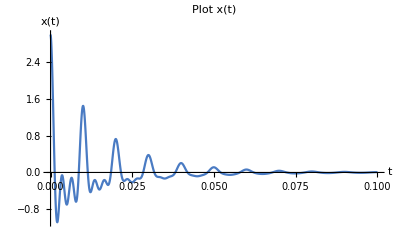

#### Compute the spectrum X(ⅇ^ⅉω)

In order to compute the spectrum, we need to use fourier transform. This is done so we can move between time domain and frequency domain. After the fourier transform is done we get H(ⅇ^ⅉω) function for frequency domain.
H(ⅇ^ⅉω) = (50+ⅈ ω)/(40000 π^2-(-50 ⅈ+ω)^2)+(75+ⅈ ω)/(160000 π^2-(-75 ⅈ+ω)^2)+(100+ⅈ ω)/(360000 π^2-(-100 ⅈ+ω)^2)

#### Plot X(ⅇ^ⅉω) and arg[X(ⅇ^ⅉω)]

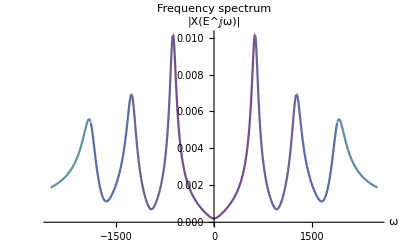
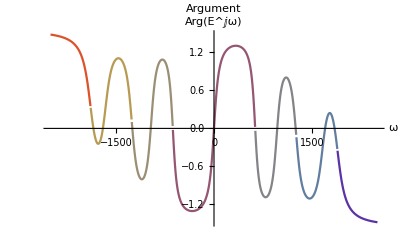

#### Find local maxima and minima, and determine where the frequencies are at

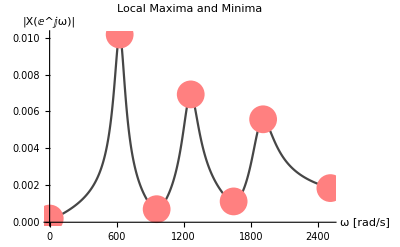
Maxima = {{627,0.0101686},{1263,0.00692622},{1911,0.00557766}}
Minima = {{1,0.000201276},{958,0.000707438},{1647,0.00112868},{2513,0.00185057}}

The plot of the local minima and maxima with with the frequencies:

-Graphics-

#### From the expression x(t), motivate the local maxima

The local maxima:s frequencies → {99.7901,201.013,304.145} are almost identical to the x(t) x(t)=(ⅇ^(-50 t)Cos[2π 100t]+ⅇ^(-75 t)Cos[2π 200t]+ⅇ^(-100 t)Cos[2π 300t])
99.7901 we can say it’s almost 100, 201.013304 is almost 200, and 304.145 is almost 300. As we see that they are almost identical we could take the maximum values direct from the signal x(t).

### Code

```mathematica
ClearAll["`*"];
SetOptions[{FourierTransform,InverseFourierTransform},FourierParameters->{1,-1}];
```

```mathematica
x[t_]=(E^(-50 t)Cos[2π 100t]+E^(-75 t)Cos[2π 200t]+E^(-100 t)Cos[2π 300t])*UnitStep[t]
```

(ⅇ^(-50 t) Cos[200 π t]+ⅇ^(-75 t) Cos[400 π t]+ⅇ^(-100 t) Cos[600 π t]) UnitStep[t]

```mathematica
Plot[x[t], {t, 0 , 0.1}, PlotRange->All,PlotLabel->"Plot x(t)", AxesLabel->{"t", "x(t)"}, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
X[ω_]=FourierTransform[x[t],t, ω]
```

(50+ⅈ ω)/(40000 π^2-(-50 ⅈ+ω)^2)+(75+ⅈ ω)/(160000 π^2-(-75 ⅈ+ω)^2)+(100+ⅈ ω)/(360000 π^2-(-100 ⅈ+ω)^2)

```mathematica
Plot[Abs[X[ω]], {ω, - 2500, 2500},AxesLabel->{"ω","|X(E^ⅉω)|"},PlotLabel->"Frequency spectrum",ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
Plot[Arg[X[ω]], {ω, - 2500, 2500},AxesLabel->{"ω","Arg(E^ⅉω)"},PlotLabel->"Argument",ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
data=Table[N[Abs[X[ω]]], {ω, 800π}];
maxima = FindPeaks[data]
maxima[[All, 1]]/N[2π]
minima=Abs[FindPeaks[Table[N[-Abs[X[ω]]], {ω, 800π}]]]
```

{{627,0.0101686},{1263,0.00692622},{1911,0.00557766}}

{99.7901,201.013,304.145}

{{1,0.000201276},{958,0.000707438},{1647,0.00112868},{2513,0.00185057}}

```mathematica
ListLinePlot[Table[N[Abs[X[ω]]], {ω, 800π}],Epilog->{Pink,PointSize[0.05],Point[Join[maxima, minima]]},PlotLabel->"Local Maxima and Minima",AxesLabel->{"ω [rad/s]","|X(ⅇ^ⅉω)|"}, ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
(*Extracting first maxima value which are the frequencies and then dividing by 2π for seeing the correct frequencies and compare them by x(t):s value
(E^(-50 t) Cos[200 π t]+E^(-75 t) Cos[400 π t]+E^(-100 t) Cos[600 π t])*)
```